```mathematica
With[{indexMapT=MapIndexed[#1->#2[[1]]&,VertexList[
VertexDelete[NearestNeighborGraph[Position[
Array[1&,{3,3}],1]],
{{1,1},{1,2},{3,1},{3,2}}]]]},
With[{SimplePegGameGraph1={{"[◼]", "NestWhileGraph"}}[
{{"[◼]", "IterateTPSMove"}}[{{2,3,4},{1,4,5}}],
{ReplacePart[Table[1,{5}],({3,3}/.indexMapT)->0]},
UnsameQ@@#&,2,AspectRatio->1/2]},Graph[SimplePegGameGraph1,
VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[indexMapT][
#2],#1,Center,#3]&),
VertexSize->1,PerformanceGoal->"Quality",EdgeStyle->Gray,
VertexCoordinates->MapIndexed[#1->{4#2[[1]],0}&,
VertexList@SimplePegGameGraph1]]]]
```

-Graphics-

```mathematica
indexMapT=MapIndexed[#1->#2[[1]]&,VertexList[
VertexDelete[NearestNeighborGraph[Position[
Array[1&,{3,3}],1]],
{{1,1},{1,2},{3,1},{3,2}}]]]
```

{{1,3}→1,{2,1}→2,{2,2}→3,{2,3}→4,{3,3}→5}

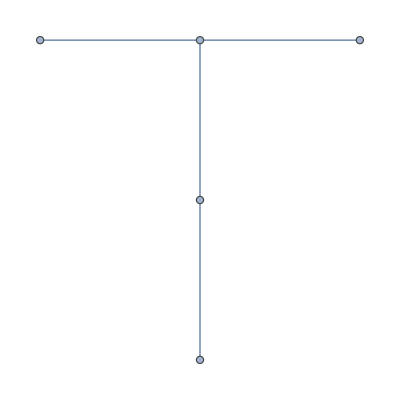

```mathematica
VertexDelete[NearestNeighborGraph[Position[
Array[1&,{3,3}],1]],
{{1,1},{1,2},{3,1},{3,2}}]
```

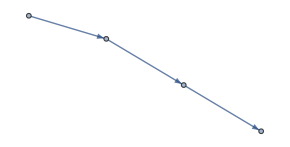

```mathematica
SimplePegGameGraph1={{"[◼]", "NestWhileGraph"}}[
{{"[◼]", "IterateTPSMove"}}[{{2,3,4},{1,4,5}}],
{ReplacePart[Table[1,{5}],({3,3}/.indexMapT)->0]},
UnsameQ@@#&,2,AspectRatio->1/2]
```

```mathematica
{ReplacePart[Table[1,{5}],({3,3}/.indexMapT)->0]}
```

{{1,1,1,1,0}}

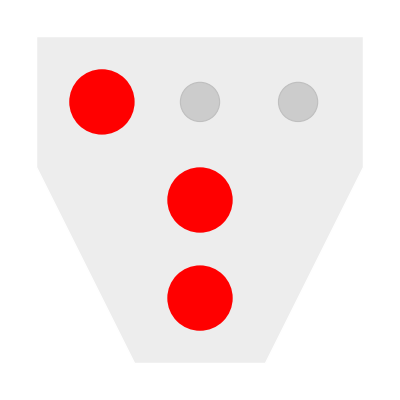

```mathematica
{{"[◼]", "PegSolitaireGraphics"}}[{{1,3}->1,{2,1}->2,{2,2}->3,{2,3}->4,{3,3}->5}][{1,1,1,0,0}]
```

```mathematica
VertexList@SimplePegGameGraph1
```

{{1,1,1,1,0},{0,1,1,0,1},{0,0,0,1,1},{1,0,0,0,0}}

```mathematica
MapIndexed[#1->{4#2[[1]],0}&,
VertexList@SimplePegGameGraph1]
```

{{1,1,1,1,0}→{4,0},{0,1,1,0,1}→{8,0},{0,0,0,1,1}→{12,0},{1,0,0,0,0}→{16,0}}

```mathematica
#2[[1]] &/@ VertexList@SimplePegGameGraph1
```

Function::slotn: Slot number 2 in #2⟦1⟧& cannot be filled from (#2⟦1⟧&)[{1,1,1,1,0}].

Function::slotn: Slot number 2 in #2⟦1⟧& cannot be filled from (#2⟦1⟧&)[{0,1,1,0,1}].

Function::slotn: Slot number 2 in #2⟦1⟧& cannot be filled from (#2⟦1⟧&)[{0,0,0,1,1}].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

{2,2,2,2}

```mathematica
indexMapT
```

{{1,3}→1,{2,1}→2,{2,2}→3,{2,3}→4,{3,3}→5}

```mathematica
With[{indexMapCross=MapIndexed[#1->#2[[1]]&,VertexList[
VertexDelete[NearestNeighborGraph[Position[
Array[1&,{4,4}],1]],{{1,1},{1,2},
{1,4},{2,4},{4,4},{4,3},{3,1},{4,1}}]]]},With[{SimplePegGameGraph2={{"[◼]", "NestWhileGraph"}}[
{{"[◼]", "IterateTPSMove"}}[{{1,4,6},{7,6,5},
{3,5,8},{4,3,2}}],
{ReplacePart[Table[1,{8}],({1,3}/.indexMapCross)->0]},
UnsameQ@@#&,2]},Graph[SimplePegGameGraph2,
VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[indexMapCross][
#2],#1,Center,#3]&),
VertexSize->1.2,PerformanceGoal->"Quality",EdgeStyle->Gray,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->3]]]
```

-Graphics-

```mathematica
{{"[◼]", "PegSolitaireGraphics"}}[{{1,3}->1,{2,1}->2,{2,2}->3,{2,3}->4,{3,3}->5}][{1,1,1,0,0}]
```

-Graphics-

```mathematica
shape[{xc_, yc_}, n_, {w_, h_}] := {{"[◼]", "PegSolitaireGraphics"}}[{{1,3}->1,{2,1}->2,{2,2}->3,{2,3}->4,{3,3}->5}][{1,1,1,0,0}]
```

```mathematica
Graph[{1<->2,2<->3},VertexShapeFunction->shape,VertexSize->0.5]
```

-Graphics-

#### PegSolitaireGraphics

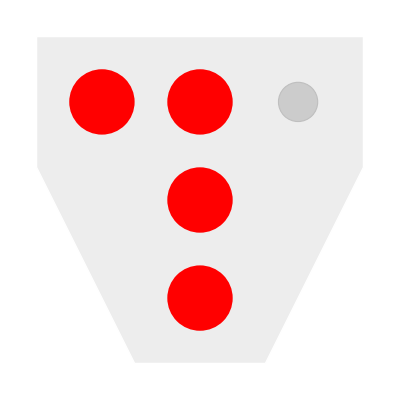

```mathematica
coords = {{1,3}->1,{2,1}->2,{2,2}->3,{2,3}->4,{3,3}->5};
states = {1,1,1,1,0};
{{"[◼]", "PegSolitaireGraphics"}}[coords][states]
```

```mathematica
Append[Table[1, Length[coords]-1],0]
```

{1,1,1,1,0}

```mathematica
startingboards[coords_]:=Table[{{"[◼]", "PegSolitaireGraphics"}}[coords][state],{state, Permutations[Append[Table[1, Length[coords]-1],0]]}]
```

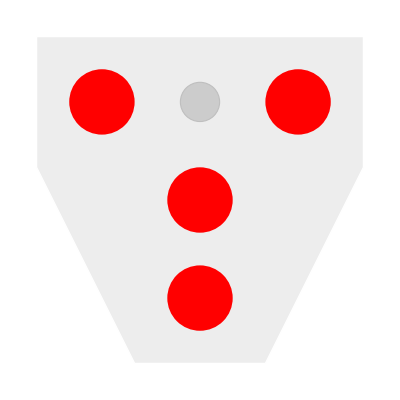
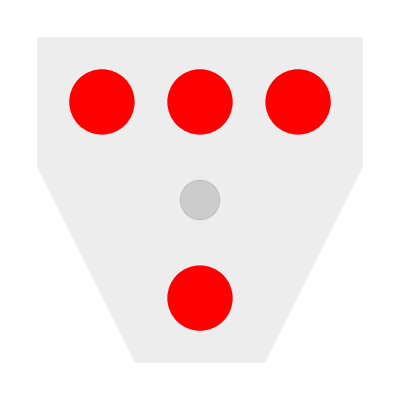
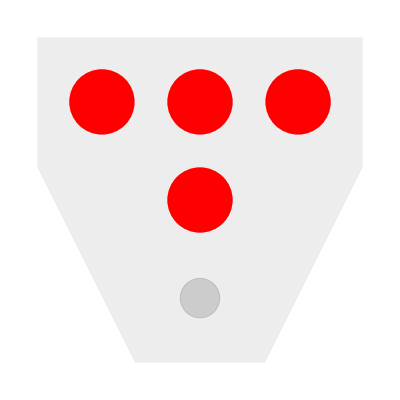
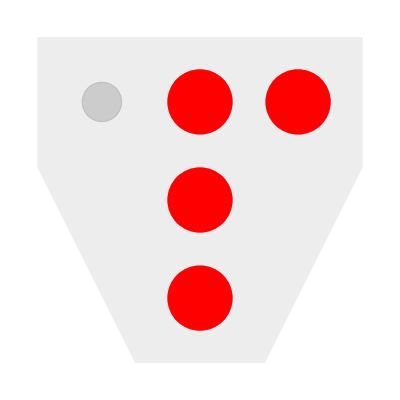
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
startingboards[{{1,3}->1,{2,1}->2,{2,2}->3,{2,3}->4,{3,3}->5}]
```

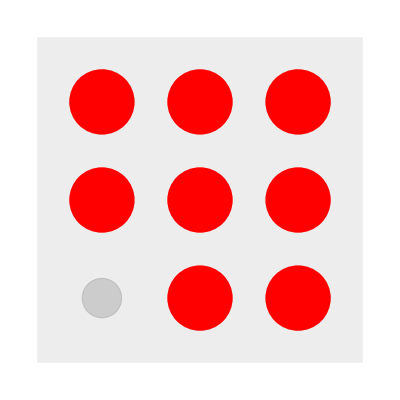
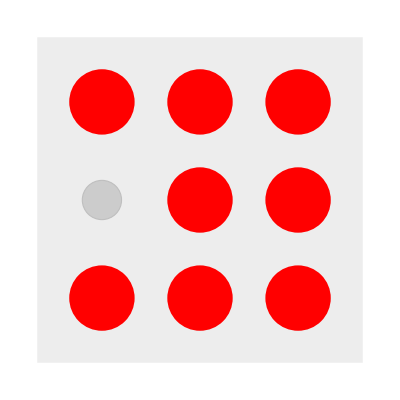
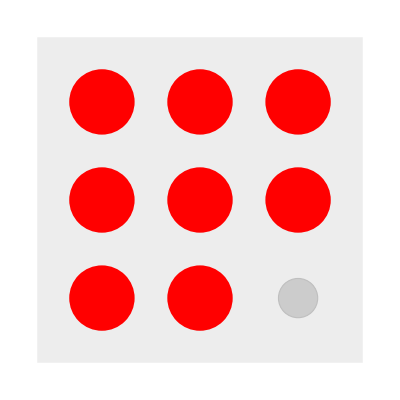
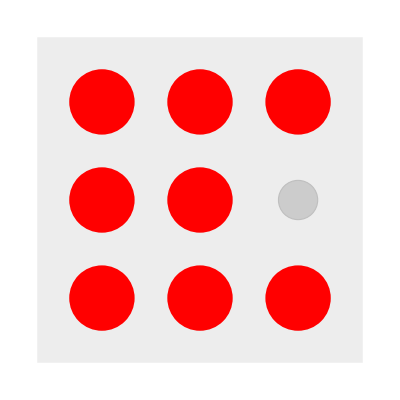
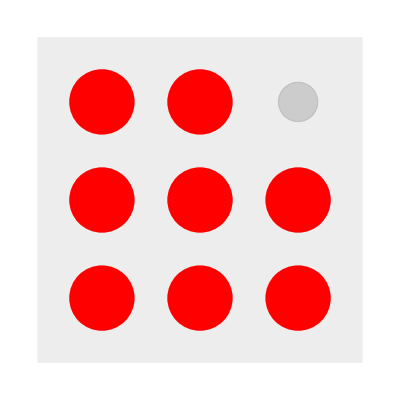
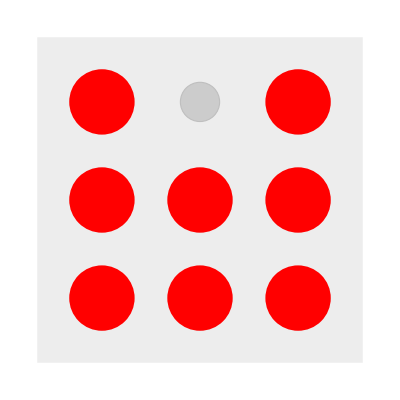
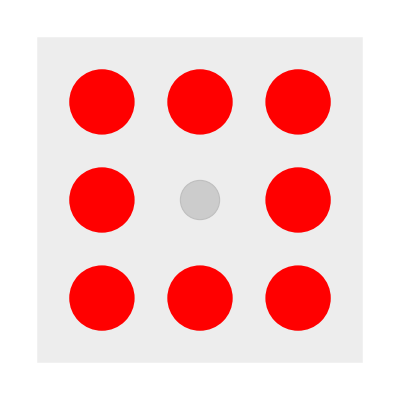
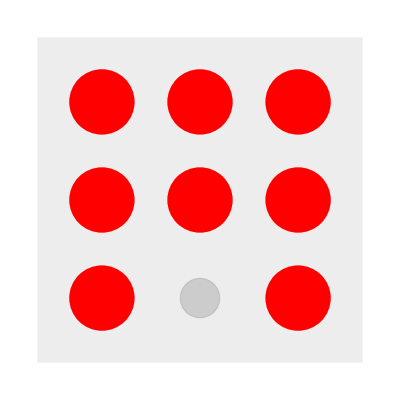

```mathematica
startingboards[{{1,3}->1,{2,1}->2,{2,2}->3,{2,3}->4,{3,3}->5,{3,2}->6,{3,1}->7,{1,2}->8,{1,1}->9}]
```

```mathematica
Graph[SimplePegGameGraph1,
VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[indexMapT][{1,1,1,0,0}],#1,Center,#3]&),
VertexSize->1,PerformanceGoal->"Quality",EdgeStyle->Gray,
VertexCoordinates->MapIndexed[#1->{4#2[[1]],0}&,
VertexList@SimplePegGameGraph1]]
```

-Graphics-

```mathematica
Inset[{{"[◼]", "PegSolitaireGraphics"}}[indexMapT][
#2],#1,Center,#3]&
```

Inset[[◼] | PegSolitaireGraphics [indexMapT][#2],#1,Center,#3]&

```mathematica
Graph[SimplePegGameGraph1,
VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[indexMapT][{1,1,1,1,0}],#1,Center,#3]&),
VertexSize->1,PerformanceGoal->"Quality",EdgeStyle->Gray,
VertexCoordinates->MapIndexed[#1->{4#2[[1]],0}&,
VertexList@SimplePegGameGraph1]]
```

-Graphics-

```mathematica
VertexList@SimplePegGameGraph1
```

{{1,1,1,1,0},{0,1,1,0,1},{0,0,0,1,1},{1,0,0,0,0}}

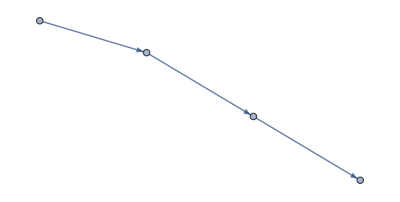

```mathematica
SimplePegGameGraph1
```

```mathematica
MapIndexed[#1->{4#2[[1]],0}&,VertexList@SimplePegGameGraph1]
```

{{1,1,1,1,0}→{4,0},{0,1,1,0,1}→{8,0},{0,0,0,1,1}→{12,0},{1,0,0,0,0}→{16,0}}